```mathematica
(* fonction de dispersion des hologrammes en mm et en pixels *)
```

```mathematica
AE=58 (* distance hologramme - CCD en mm *)
```

58

```mathematica
pixel=0.024 (* en mm *)
```

0.024

```mathematica
lambda0=656 (* longueur d'onde connue en nm *)
```

656

```mathematica
AB0pix=600 (* pour cette longueur d'onde, écart à l'ordre 0 en pixels *)
```

600

```mathematica
AB0=AB0pix*0.024 (* en mm *)
```

14.4

```mathematica
g=(1000000)/lambda0*(AB0/AE)/Sqrt[1+(AB0/AE)^2] (* nombre de traits/mm *)
```

367.318

```mathematica
a=1/g (* pas du réseau en mm *)
```

0.00272244

```mathematica
AB[lambda_]:=AE*(lambda/a/1000000)/Sqrt[1-(lambda/a/1000000)^2]/pixel (* pixels en fontion de nm *)
```

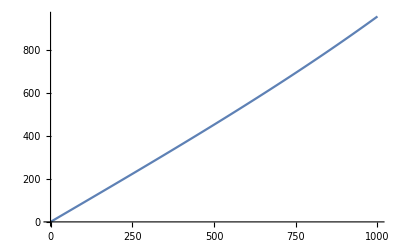

```mathematica
Plot[AB[lambda],{lambda,0,1000}]
```

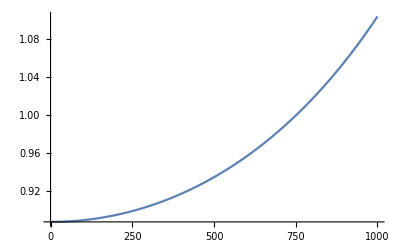

```mathematica
Plot[AB'[lambda],{lambda,0,1000} ](* dérivée -> pixel/nm en fonction de lambda *)
```

```mathematica
(* calcul de la résolution en nm/pixels *)
res= Sin[ArcTan[(pix+e/2)/DD] ]/pas- Sin[ArcTan[(pix-e/2)/DD] ]/pas
```

-(-e/2+pix)/(DD pas √(1+(-e/2+pix)^2/DD^2))+(e/2+pix)/(DD pas √(1+(e/2+pix)^2/DD^2))

```mathematica
Series[res,{e,0,2}]//FullSimplify
```

(DD^3 √(1+pix^2/DD^2) e)/(pas (DD^2+pix^2)^2)+O[e]^3

```mathematica
e*(Tan[i]-Tan[ArcSin[Sin[i]/n]])//FullSimplify
```

e (-Sin[i]/(n √(1-Sin[i]^2/n^2))+Tan[i])